# Opacity anaylsis

## Measurement

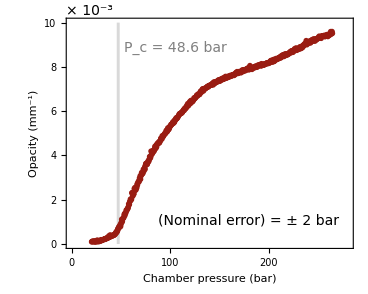

```mathematica
(* -- import data -- *)
raw=Import[NotebookDirectory[]<>"data/opacity.mx"]; (* [mm^-1] *)

(* -- plot -- *)
gfa=ListLinePlot[

raw,

Prolog->{{FaceForm[{LightGray,Opacity[1]}],EdgeForm[Transparent],Rectangle[{48.630-3,0},{48.630,.01}]}},

Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Text[Style["P_c = 48.6 bar",{FontColor->Gray,FontSize->14,FontWeight->Plain}],Scaled@{.2,.9},{-1,1}],
Text[Style["(Nominal error) = ± 2 bar",{FontColor->Black,FontSize->14,FontWeight->Plain}],Scaled@{.95,.15},{1,1}],
Text[Style["× 10^-3",{FontColor->Black,FontSize->14,FontWeight->Plain}],Scaled[{0,1}],{-1,-1}]
},

Joined->True,
ScalingFunctions->"Linear",

PlotRange->{{0,280},{0,.01}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{RGBColor[.60,.11,.07],Opacity[1],AbsoluteThickness[1]},

PlotMarkers->{
Graphics[{RGBColor[.60,.11,.07,.05],Disk[{0,0},Offset[3]]}]
},

Frame->True,
FrameTicks->{
{Table[{i/10^3,i,{.015,0}},{i,0,10,2}],
Table[{i/10^3,Null,{.015,0}},{i,0,10,2}]},
Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,270,50}]ᵀ
},
FrameLabel->{{"Opacity (mm^-1)",None},{"Chamber pressure (bar)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->Full,
GridLinesStyle->Directive[{Gray,Opacity[1],AbsoluteThickness[1]}],

ImagePadding->{{55,55},{50,20}},
ImageSize->(130/2*2)*(72/25.4),
AspectRatio->.8

];

Print[gfa];
```

## Refractive index of Ar medium and clusters

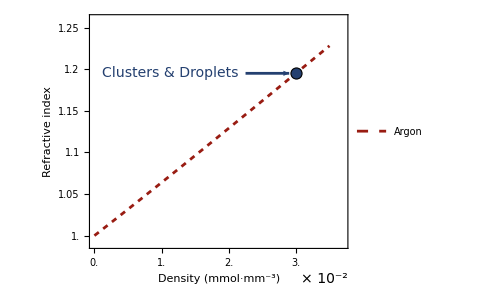

```mathematica
(* -- density ρ to refractive index n -- *)
coff[ρ_]:=4.1960ρ+1.74ρ^2-85.9ρ^3-350ρ^4; (* ρ in [mmol/mm^3] *)
nFunc[ρ_]:=√((2coff[ρ]+1)/(1-coff[ρ]));
dt=Table[{ρ,nFunc[ρ]},{ρ,0,.035,.001}];
pt={ρ,nFunc[ρ]}/.ρ->.3*^-1;

(* -- plot -- *)
gfb=ListPlot[

dt,

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Text[Style["× 10^-2",{FontColor->Black,FontSize->14,FontWeight->Plain}],Scaled[{1,-.1}],{1,1}],
{EdgeForm[Transparent],FaceForm[{RGBColor[.14,.25,.44,1]}],Disk[pt,Offset[4]]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[2],Arrowheads[{0,.05}],Arrow[{pt-{.0075,0},pt-{.001,0}}]},
Text[Style["Clusters & Droplets",{FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain}],pt-{.0085,0},{1,0}]
},

Joined->True,
ScalingFunctions->"Linear",

PlotRange->{{0,.037},{.99,1.26}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{RGBColor[.60,.11,.07],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[4]},

PlotLegends->Placed[
LineLegend[
{"Argon"},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->"Row"],
{Scaled@{.95,.05},{1,0}}],

Frame->True,
FrameTicks->{
{Table[{i,i,{.015,0}},{i,1,1.3,.05}],
Table[{i,Null,{.015,0}},{i,1,1.3,.05}]},
{Table[{i/100,i,{.015,0}},{i,0,3.7,.5}],
Table[{i/100,Null,{.015,0}},{i,0,3.7,.5}]}
},
FrameLabel->{{"Refractive index",None},{"Density (mmol·mm^-3)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->Full,
GridLinesStyle->Directive[{Gray,Opacity[1],AbsoluteThickness[1]}],

ImagePadding->{{55,55},{50,20}},
ImageSize->(130/2*2)*(72/25.4),
AspectRatio->.8

];

Print[gfb];
```

## Rayleigh scattering by clusters

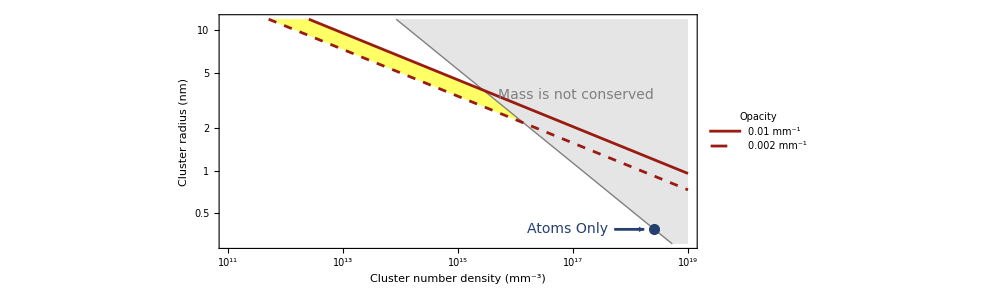

```mathematica
(* -- equations -- *)
λ=633*^-6; (* [mm] *)
n=1.2; (* approx. *)
nAr=2.6*^18; (* [mm^-3] argon number density from NIST (100 bar, 294 K) *)
ρc=6.022*^20*0.03; (* [mm^-3] internal density of a cluster *)
σ[r_]:=(2^7 π^5)/3 r^6/λ^4((n^2-1)/(n^2+2))^2; (* [mm^2] *)
opacity[n_,r_]:=n σ[r]; (* [mm^-1] *)

(* -- plot -- *)
dt=Table[
sol=Table[NSolve[opacity[numDens,r]==i&&r>0,r][[1]],{i,{.01,.002}}];
{
{numDens,r*10^6}/.sol[[1]],
{numDens,r*10^6}/.sol[[2]]
},
{numDens,PowerRange[10^11,10^19,√10.]}
]ᵀ;
boundary=Table[
{numDens,(nAr/(numDens*ρc))^(1/3)*10^6},
{numDens,PowerRange[10^11,10^19,√10.]}];

(* -- points -- *)
pts={
{numDens,r}/.FindRoot[{opacity[numDens,r*10^-6]==.01,r==12},{{numDens,10^13},{r,12}}],
{numDens,r}/.FindRoot[{opacity[numDens,r*10^-6]==.002,r==12},{{numDens,10^13},{r,12}}],
{numDens,r}/.FindRoot[{opacity[numDens,r*10^-6]==.002,(nAr/(numDens*ρc))==(r*10^-6)^3},{{numDens,10^16},{r,2}}],
{numDens,r}/.FindRoot[{opacity[numDens,r*10^-6]==.01,(nAr/(numDens*ρc))==(r*10^-6)^3},{{numDens,10^16},{r,2}}]
};

gfc=ListLinePlot[

{boundary,dt[[1]],dt[[2]]},

Prolog->{
{RGBColor[1,1,0,.6],Polygon[Log@pts]}
},

Epilog->{
Text[Style["c",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Text[Style["Mass is not conserved",{FontColor->Gray,FontSize->14,FontWeight->Plain}],Log@{10^18.4,3.1},{1,-1}],
Text[Style["Atoms Only",{FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain}],Log@{nAr/6.3,10^6*ρc^(-1/3)},{1,0}],
{RGBColor[.14,.25,.44,1],Disk[Log@{nAr,10^6*ρc^(-1/3)},Offset[4]]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[2],Arrowheads[{0,.025}],Arrow[Log@{{nAr/5,10^6*ρc^(-1/3)},{nAr/1.5,10^6*ρc^(-1/3)}}]}
},

PlotRange->{{10^11,10^19},{.3,12}},
PlotRangePadding->0,
PlotRangeClipping->False,

ScalingFunctions->{"Log","Log"},

Joined->True,
PlotStyle->{
{Gray,AbsoluteThickness[1]},
{RGBColor[.60,.11,.07,1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],AbsoluteThickness[2],AbsoluteDashing[6]}
},
PlotMarkers->None,

LabelStyle->{FontFamily->"Arial",FontSize->14,FontColor->Black},

PlotLegends->Placed[
LineLegend[
{{},Directive[{RGBColor[.60,.11,.07,1],AbsoluteThickness[2]}],
Directive[{RGBColor[.60,.11,.07,1],AbsoluteThickness[2],AbsoluteDashing[6]}]},
{None,"0.01 mm^-1","0.002 mm^-1"},
LegendMarkerSize->{{36,12}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendLabel->"Opacity",
LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1]]]&),
LegendMarkers->None,
LegendMargins->1,LegendLayout->"Column"],
{Scaled@({.625,1}*.05),{0,0}}],

Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1]],
FrameLabel->{{"Cluster radius (nm)","Number of atoms per cluster"},{"Cluster number density (mm^-3)","Ratio to argon atom density (at 100 bar, 294 K)"}},

FrameTicks->{
{Table[{i,i,{.015,0}},{i,{.5,1,2,5,10}}],
Table[{10^6*(10^i/ρc)^(1/3),Superscript[10,i],{.015,0}},{i,0,4}]},
{Table[{10^i,Superscript[10,i],{.015,0}},{i,10,20,2}],
Table[{(10^i)*nAr,Superscript[10,i],{.015,0}},{i,-8,1,2}]}
},

Filling->{1->Top},

GridLines->Full,
GridLinesStyle->Directive[{Gray,Opacity[1],AbsoluteThickness[.5]}],

ImagePadding->{{55,55},{50,50}},
ImageSize->(130*2)*(72/25.4),
AspectRatio->.4

];

Print[gfc];
```

## Merge figures

```mathematica
gf=Grid[{{gfa,gfb},{gfc,SpanFromLeft}},Spacings->0];
Print[gf];

Export[NotebookDirectory[]<>"opacity.pdf",gf];
```

-Graphics- | -Graphics-
-Graphics- |